# COMPUTATION OF CROSS SECTION FOR SUBLEADING TWIST DIS with JET MASS with no transverse momentum

## PRELIMINARIES

#### LOAD FEYNCALC PACKAGE

```mathematica
<<HighEnergyPhysics`fc`
```

Set::wrsym: Symbol TraditionalForm`MonomialList is Protected.

DumpGet::bgbf: File TraditionalForm`"/Users/bacchett/Library/Mathematica/Applications/HighEnergyPhysics/Tarcer/tarcer25.mx" cannot be loaded, it is corrupted or is written on a different machine.

```mathematica
ClearScalarProducts
```

#### SOME DEFINITIONS

```mathematica
Unit={nm,np,ni,nj};
Trans={St,Aht};

eta=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});

GAp = GS[nm]; 
GAm = GS[np]; 
GA5 = DiracGamma[5]; 
GAT = -(GS[ni]FV[ni,α]+GS[nj]FV[nj,α]);

gpperp=MT[μ,ν]-FV[np,μ]FV[nm,ν]-FV[nm,μ]FV[np,ν];
eppsperp=Contract[LC[ρ,σ,μ,ν]FV[np,ρ] FV[nm,σ]];

epsT[epsT[v_]]=-v;
epsT[0]=0;
```

#### SCALAR PRODUCTS

```mathematica
Table[ScalarProduct[Unit[[i]],Unit[[j]]]=eta[[i,j]],{i,1,4},{j,1,4}];
Table[ScalarProduct[Trans[[i]],Unit[[j]]]=0,{i,1,Length[Trans]},{j,1,2}];
Table[ScalarProduct[epsT[Trans[[i]]],Unit[[j]]]=0,{i,1,Length[Trans]},{j,1,2}];

epsreduce=Eps[a_,b_,c_,d_]->Sum[Inner[Pair,{a,b,c,d},Permutations[{Momentum[nm],Momentum[np],Momentum[ni],Momentum[nj]}][[i]],Times](Signature[Permutations[{nm,np,ni,nj}][[i]]]),{i,1,24}];
```

Set::setraw: Cannot assign to raw object TraditionalForm`1.

#### FORMATTING INSTRUCTIONS

```mathematica
Format[CC[y_],TraditionalForm]:="C(y)";

Format[Ahl,TraditionalForm]:=Subscript[A, hL];
Format[Aht,TraditionalForm]:=Subscript[A, hT];
Format[ϕAht,TraditionalForm]:=Subscript[ϕ, Subscript[A, h]];
Format[Sl,TraditionalForm]:=Subscript[S, L];
Format[St,TraditionalForm]:=Subscript[S, T];
Format[Mh,TraditionalForm]:=Subscript[M, h];
Format[Mj,TraditionalForm]:=Subscript[M, j];
Format[mq,TraditionalForm]:=Subscript[m, q];

Format[f1,TraditionalForm]:=Subscript[f, 1];
Format[g1,TraditionalForm]:=Subscript[g, 1];
Format[h1,TraditionalForm]:=Subscript[h, 1];
Format[hL,TraditionalForm]:=Subscript[h, L];
Format[fT,TraditionalForm]:=Subscript[f, T];
Format[gT,TraditionalForm]:=Subscript[g, T];
Format[ftilT,TraditionalForm]:=Subscript[f̃, T];
Format[gtilT,TraditionalForm]:=Subscript[g̃, T];
Format[ee,TraditionalForm]:=e;
Format[eL,TraditionalForm]:=Subscript[e, L];
Format[D1,TraditionalForm]:=Subscript[D, 1];
Format[G1,TraditionalForm]:=Subscript[G, 1];
Format[H1,TraditionalForm]:=Subscript[H, 1];
Format[DtilT,TraditionalForm]:=Subscript[D̃, T];
Format[GtilT,TraditionalForm]:=Subscript[G̃, T];
Format[Htil,TraditionalForm]:=H̃;
Format[HtilL,TraditionalForm]:=Subscript[H̃, L];
Format[Etil,TraditionalForm]:="Ẽ";
Format[EtilL,TraditionalForm]:="(Ẽ)_L";
Format[gperp,TraditionalForm]:=g_∟;
Format[epsperp,TraditionalForm]:=ϵ_∟;
Format[epsT,TraditionalForm]:=Subscript[ϵ, T];
Format[fQ2Mttsmu ,TraditionalForm]:="(2  M SuperscriptBox[tt, {μ])/Q";Format[fQ2iMttamu ,TraditionalForm]:= "ⅈ (2 M SuperscriptBox[tt, [μ])/Q";
Format[munugperp[St_,Aht_],TraditionalForm]:=Pair[LorentzIndex["{μ"],Momentum[St]] Pair[LorentzIndex["ν}"],Momentum[Aht]]- g_∟[LorentzIndex[μ],LorentzIndex[ν]] Pair[Momentum[Aht],Momentum[St]];
```

#### LEPTONIC TENSOR

```mathematica
Lept=Q^2/y^2(-2A[y]gpperp+4 B[y] 1/2(FV[nm,μ]+FV[np,μ])(FV[nm,ν]+FV[np,ν])+4 B[y](FV[ni,μ]FV[ni,ν]+1/2 gpperp)-2ⅈ λ CC[y]eppsperp+V[y]2Symmetrize[1/(√2)(FV[nm,μ]+FV[np,μ])FV[ni,ν],{μ,ν}]
-2ⅈ λ W[y]AntiSymmetrize[-1/(√2)(FV[nm,ν]+FV[np,ν])Contract[eppsperp FV[ni,ν]],{μ,ν}]);
```

## SUBLEADING TWIST, JET, WITHOUT TRANSVERSE MOMENTUM

#### DISTRIBUTION QUARK-QUARK CORRELATION FUNCTIONS

See Eq. 3.31 of JHEP.

```mathematica
Phi=1/2(f1 +Sl  g1  GA5+ h1  GA5 .GS[St]).GAm+M/(2Pplus)  (ee+gT   GA5 .GS[St]  +ⅈ Sl  hL  GA5 . DiracSigma[GS[nm],GS[np]]);

Phialfad= M/2 (f1Tp1  FV[epsT[St],α]. GAm+ g1T1 FV[St,α]. GA5.GAm- h1Lp1 Sl GA5.GAT.GAm-ⅈ h1p1 GAT.GAm);
```

```mathematica
(*Pplus=(√2 Q)/(2x)*)
```

#### JET QUARK-QUARK CORRELATION FUNCTION

From our calculations

```mathematica
Delta=1/2 GAp+ Mj/(2 lmin) +Mj2/(4 lmin^2)GAm;

Deltaalfad=0;

Deltatilalfa=GAT;

(*lmin=(2 Q)/(2x)*)
```

#### DISTRIBUTION QUARK-GLUON-QUARK CORRELATORS

See Eq. 3.45 of JHEP without transverse momentum.

```mathematica
PhialfaA=M/2(- x ftilT FV[epsT[St],α].GAm+ x gtilT FV[St,α].GA5.GAm+1/2(x htilL+ⅈ x etilL)Sl GA5.GAT.GAm+1/2(-x etil +ⅈ x htil)GAT.GAm);

PhialfaD=PhialfaA+Phialfad;
```

#### JET QUARK-GLUON-QUARK CORRELATOR

```mathematica
DeltaalfaA=-(Mj-mq)/4 GAT.GAp;
DeltaalfaD=DeltaalfaA+Deltaalfad
```

#### FIRST PART OF HADRONIC TENSOR - FOLLOWING TMD FORMULA

```mathematica
MWW1a= Tr[Phi.GA[μ].Delta .GA[ν]]/.{Pplus-> Q/(√2 x),lmin->Q/(√2) }
```

4 ((e M x M_j g^μν)/(2 Q^2)-1/4 f_1 g^μν+(f_1 Mj2 np^μ np^ν)/(2 Q^2)+1/4 f_1 nm^ν np^μ+1/4 f_1 nm^μ np^ν-1/4 ⅈ g_1 S_L ϵ^μνnmnp-(ⅈ M Mj2 x g_T ϵ^(μνnp S_T))/(2 √2 Q^3)-(ⅈ M x g_T ϵ^(μνnm S_T))/(2 √2 Q)+(ⅈ M x h_L M_j S_L ϵ^μνnmnp)/(2 Q^2)+(ⅈ h_1 M_j ϵ^(μνnp S_T))/(2 √2 Q))

Neglect terms of order M^2/Q^2 (or higher)

```mathematica
MWW1=MWW1a//Series[#,{Q,∞,1}]&//Normal//Collect[#,{f1,g1},Simplify]&
```

f_1 (-g^μν+nm^ν np^μ+nm^μ np^ν)-(ⅈ √2 (M x g_T ϵ^(μνnm S_T)-h_1 M_j ϵ^(μνnp S_T)))/Q-ⅈ g_1 S_L ϵ^μνnmnp

The f1 and g1 terms are ok. The gT and h1 terms are not ELM gauge invariant.

#### MIDDLE PART OF HADRONIC TENSOR - FOLLOWING TMD FORMULA

```mathematica
MWW1B=1/(√2 Q) Tr[Phialfad.GA[μ].Deltatilalfa .GA[ν]]/.{Pplus-> Q/(√2 x),lmin->Q/(√2) }//Collect[#,{f1Tp1,g1T1},Simplify]&
```

-(√2 f1Tp1 M (np^ν (ni^μ ni·ϵ_T(S_T)+nj^μ nj·ϵ_T(S_T))+np^μ (ni^ν ni·ϵ_T(S_T)+nj^ν nj·ϵ_T(S_T))))/Q+(ⅈ √2 g1T1 M (ni·S_T ϵ^μνninp+nj·S_T ϵ^μνnjnp))/Q

#### LAST PART OF HADRONIC TENSOR

Notice that I have to change sign to the DeltaalfaA term in the complex - conjugate term. This is due to the hermiticity properties and it is analogous to the sign change in etil in the PhialfaA contribution

```mathematica
MWW2a= (-Tr[GA[α].(GAm/(Q √2)).GA[ν].PhialfaA.GA[μ].Delta ]-Tr[GA[μ].(GAm/(Q √2)).GA[α].Delta.GA[ν].(PhialfaA/.{ⅈ-> -ⅈ,-ⅈ->ⅈ,etil-> -etil, htil-> -htil})]-Tr[GA[ν].(GAp/(Q √2)).GA[α].Phi.GA[μ].(-DeltaalfaA/.{ⅈ-> -ⅈ,-ⅈ->ⅈ}) ]-Tr[GA[α].(GAp/(Q √2)).GA[μ].DeltaalfaA.GA[ν].Phi])/.{Pplus-> Q/(√2 x),lmin->Q/(√2) }//Series[#,{Q,∞,1}]&//Normal[#]&//Collect[#,{h1,ftilT,gtilT},Simplify]&
```

-(√2 M x (f̃)_T (np^ν (ϵ_T(S_T))^μ+np^μ (ϵ_T(S_T))^ν))/Q+(ⅈ √2 M x (g̃)_T ϵ^(μνnp S_T))/Q+1/Q ⅈ √2 h_1 (M_j-m_q) (-nm^μ ni·S_T ϵ^νninmnp-ni^μ ϵ^(νninm S_T)-ni·S_T ϵ^μνninm-nm^μ nj·S_T ϵ^νnjnmnp-nj^μ ϵ^(νnjnm S_T)-nj·S_T ϵ^μνnjnm-2 nm^μ ϵ^(νnmnp S_T)+ϵ^(μνnm S_T))

Apply EoM relation to (g̃)_T and (f̃)_T. See Eq. (35) of our WW work

```mathematica
MWW2=MWW2a/.{ftilT-> 1/x f1Tp1,gtilT->  gT -1/x g1T1- mq/(x M)h1}//Collect[#,{h1,ftilT,gtilT},Simplify]&
```

(√2 M (-f1Tp1 (np^ν (ϵ_T(S_T))^μ+np^μ (ϵ_T(S_T))^ν)-ⅈ (g1T1-x g_T) ϵ^(μνnp S_T)))/Q-1/Q ⅈ √2 h_1 ((M_j-m_q) (nm^μ ni·S_T ϵ^νninmnp+ni^μ ϵ^(νninm S_T)+ni·S_T ϵ^μνninm+nm^μ nj·S_T ϵ^νnjnmnp+nj^μ ϵ^(νnjnm S_T)+nj·S_T ϵ^μνnjnm+2 nm^μ ϵ^(νnmnp S_T))+(m_q-M_j) ϵ^(μνnm S_T)+m_q ϵ^(μνnp S_T))

Let us focus anyway on the gT and h1 terms.

```mathematica
((MWW1/.{f1->0, g1->0}) +( MWW2/.{g1T1->0,f1Tp1->0, g1T1->0}))//Collect[#,{gT,h1},Simplify]&
```

1/Q ⅈ √2 h_1 (M_j-m_q) (-nm^μ ni·S_T ϵ^νninmnp-ni^μ ϵ^(νninm S_T)-ni·S_T ϵ^μνninm-nm^μ nj·S_T ϵ^νnjnmnp-nj^μ ϵ^(νnjnm S_T)-nj·S_T ϵ^μνnjnm-2 nm^μ ϵ^(νnmnp S_T)+ϵ^(μνnm S_T)+ϵ^(μνnp S_T))-(ⅈ √2 M x g_T (ϵ^(μνnm S_T)-ϵ^(μνnp S_T)))/Q

It is not immediately transparent that the two terms have the same structure (and gauge invariant). However, if we expand the antisymmetric tensors :

```mathematica
%/.epsreduce//Collect[#,{gT,h1},Simplify]&
```

(ⅈ √2 M x g_T ((nm^ν+np^ν) (nj^μ ni·S_T-ni^μ nj·S_T)+nm^μ (ni^ν nj·S_T-nj^ν ni·S_T)+np^μ (ni^ν nj·S_T-nj^ν ni·S_T)))/Q+(ⅈ √2 h_1 (M_j-m_q) ((nm^ν+np^ν) (nj^μ ni·S_T-ni^μ nj·S_T)+nm^μ (ni^ν nj·S_T-nj^ν ni·S_T)+np^μ (ni^ν nj·S_T-nj^ν ni·S_T)))/Q

Now the expression is gauge invariant [q is orthogonal to (nm + np)] and it is evident that gT and h1 end up in the same structure function.

## Numerical estimates

```mathematica
LogLinearPlot[Table[1/2 m/M(4/9 x(myTranu[x,i]-NIntegrate[myTranu[x,i],{y,x,1}])+1/9 x(myTrand[x,i]-NIntegrate[myTrand[x,i],{y,x,1}]))/.{m->0.3,M->0.938},{i,15,18}],{x,0.01,0.99},PlotPoints->50,PerformanceGoal->"Speed"]
```

### replica Marco 2.4gev2

```mathematica
tempBand=ReadList["/Users/bacchett/Documents/Mathematica/Plot_transversity_1112/fit_bands_ultra.out",{Number,Number,Number,Number,Number}];

NRepl=tempBand//Last//First;
Nx=Round[Length[tempBand]/NRepl];

xuvBandList=Table[Select[tempBand,#[[1]]==i&][[All,{2,4}]],{i,1,NRepl}];
xdvBandList=Table[Select[tempBand,#[[1]]==i&][[All,{2,5}]],{i,1,NRepl}];
Nex=Round[0.16 NRepl];
Nin=NRepl-2 Nex;
UU=Table[Drop[Drop[Sort[Transpose[xuvBandList][[i]]],Nex],-Nex],{i,1,Nx}]//Transpose;
DD=Table[Drop[Drop[Sort[Transpose[xdvBandList][[i]]],Nex],-Nex],{i,1,Nx}]//Transpose;
Min$xh1u[x_]:= Interpolation[UU[[1]]][x];
Max$xh1u[x_]:=Interpolation[UU[[Length[UU]]]][x];
Min$xh1d[x_]:= Interpolation[DD[[1]]][x];
Max$xh1d[x_]:=Interpolation[DD[[Length[DD]]]][x];
```

```mathematica
MassH1Prot=Table[{xuvBandList[[i,j,1]],m/M(4/9 xuvBandList[[i,j,2]]/xuvBandList[[i,j,1]]+1/9 xdvBandList[[i,j,2]]/xdvBandList[[i,j,1]])/.{m->0.,M->0.938}},{i,1,NRepl},{j,1,Length[xuvBandList[[1]]]}];

MassH1Neut=Table[{xuvBandList[[i,j,1]],m/M(1/9 xuvBandList[[i,j,2]]/xuvBandList[[i,j,1]]+4/9 xdvBandList[[i,j,2]]/xdvBandList[[i,j,1]])/.{m->0.5,M->0.938}},{i,1,NRepl},{j,1,Length[xuvBandList[[1]]]}];
```

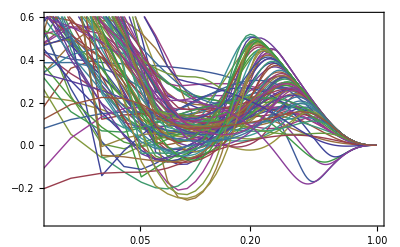

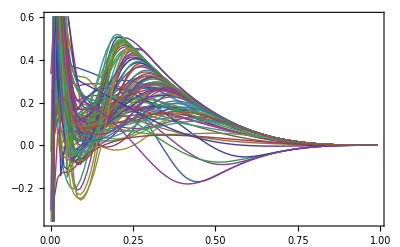

```mathematica
ListLogLinearPlot[Table[MassH1Prot[[i]]/.{m->0.5,M->0.938},{i,1,100}],Joined->True,Frame->True]
ListPlot[Table[MassH1Prot[[i]]/.{m->0.5,M->0.938},{i,1,100}],Joined->True,Frame->True]
```

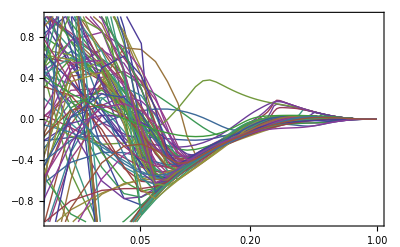

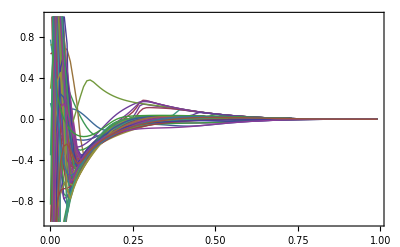

```mathematica
ListLogLinearPlot[Table[MassH1Neut[[i]]/.{m->0.5,M->0.938},{i,1,100}],PlotRange->{-1,1},Joined->True,Frame->True]
ListPlot[Table[MassH1Neut[[i]]/.{m->0.5,M->0.938},{i,1,100}],PlotRange->{-1,1},Joined->True,Frame->True]
```

### Analitic form at 1 GeV

```mathematica
ReadParam=ReadList["/Users/bacchett/Documents/Mathematica/NeuralNet/Marco/poli_x_testfunct/x^0.5_poli_x3/100replicas random in/param.out",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];

ChiSq=ReadList["/Users/bacchett/Documents/Mathematica/NeuralNet/Marco/poli_x_testfunct/x^0.5_poli_x3/100replicas random in/chisquares.out",{Number,Number,Number}];
```

```mathematica
paramVec={auv,buv,cuv,duv,adv,bdv,cdv,ddv};
FitReplex=Table[Thread[paramVec->ReadParam[[All,{2,3,4,5,6,7,8,9}]][[i]]],{i,1,NRepl}];
```

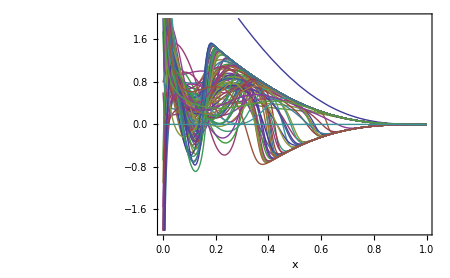

```mathematica
Plot[Evaluate[{xuv$SBDSSVLO[x]/x,Table[Tooltip[4/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+1/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x,i],{i,1,100}],0}],{x,0.001,1},PerformanceGoal->"Speed",PlotRange->{-2,2},ImageSize->{450,300},Frame->True,PlotPoints->30,BaseStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],AxesOrigin->{0,0},FrameLabel->{"x","","h_1^u_v(x)",""},LabelStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],FrameTicks->{Automatic,Automatic,None,None},Epilog->{(*Text["9% th. unc.",{-5,0.31}],*)Text["Preliminary",{-5,0.45}]}]
```

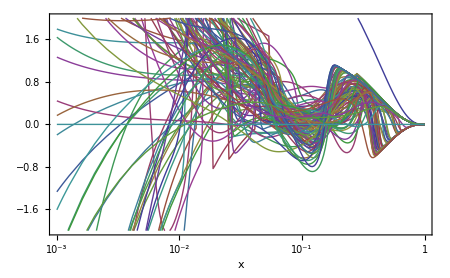

```mathematica
LogLinearPlot[Evaluate[{xuv$SBDSSVLO[x]/x,Table[Tooltip[4/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+1/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,i],{i,1,100}],0}],{x,0.001,1},PerformanceGoal->"Speed",PlotRange->{-2,2},ImageSize->{450,300},Frame->True,PlotPoints->30,BaseStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],AxesOrigin->{0,0},FrameLabel->{"x","","h_1^u_v(x)",""},LabelStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],FrameTicks->{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},1},Automatic,None,None},Epilog->{(*Text["9% th. unc.",{-5,0.31}],Text["Preliminary",{-5,0.45}]*)}]
```

### Mean values

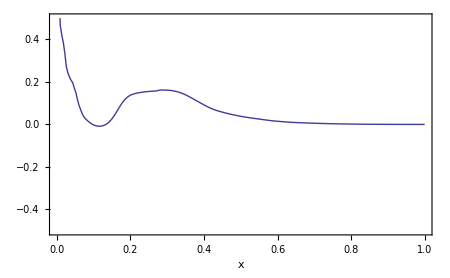

```mathematica
Plot[0.25/1 Mean[Table[4/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+1/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{x,0.001,1},PerformanceGoal->"Speed",PlotRange->{-0.5,0.5},ImageSize->{450,300},Frame->True,PlotPoints->30,BaseStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],AxesOrigin->{0,0},FrameLabel->{"x","","M_j/M∑e_q^2h_1(x), proton",""},LabelStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],FrameTicks->{Automatic,Automatic,None,None},Epilog->{(*Text["9% th. unc.",{-5,0.31}],Text["Preliminary",{-5,0.45}]*)}]
```

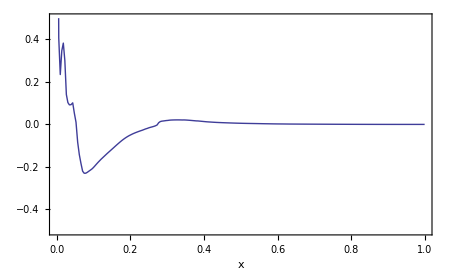

```mathematica
Plot[0.25/1 Mean[Table[1/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+4/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{x,0.001,1},PerformanceGoal->"Speed",PlotRange->{-0.5,0.5},ImageSize->{450,300},Frame->True,PlotPoints->30,BaseStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],AxesOrigin->{0,0},FrameLabel->{"x","","M_j/M∑e_q^2h_1(x),neutron",""},LabelStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],FrameTicks->{Automatic,Automatic,None,None},Epilog->{(*Text["9% th. unc.",{-5,0.31}],Text["Preliminary",{-5,0.45}]*)}]
```

### 68 % bands and mean

```mathematica
Nex=Round[0.05 NRepl];

Mjh1SumProtMin=Table[{x,0.25Take[Sort[Table[4/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+1/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{-(Nex+1)}][[1]]},{x,0.01,1,0.01}];

Mjh1SumProtMax=Table[{x,0.25 Take[Sort[Table[4/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+1/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{(Nex+1)}][[1]]},{x,0.01,1,0.01}];

Mjh1SumNeutMin=Table[{x,0.25Take[Sort[Table[1/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+4/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{-(Nex+1)}][[1]]},{x,0.01,1,0.01}];

Mjh1SumNeutMax=Table[{x,0.25 Take[Sort[Table[1/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+4/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{(Nex+1)}][[1]]},{x,0.01,1,0.01}];
```

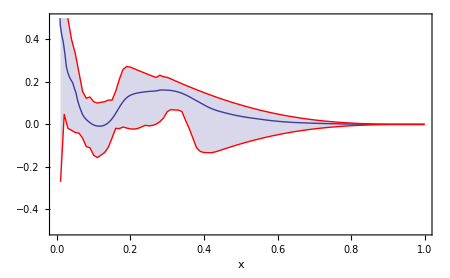

```mathematica
Show[Plot[0.25/1 Mean[Table[4/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+1/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{x,0.001,1},PerformanceGoal->"Speed",PlotRange->{-0.5,0.5},ImageSize->{450,300},Frame->True,PlotPoints->30,BaseStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],AxesOrigin->{0,0},FrameLabel->{"x","","M_j/M∑e_q^2h_1(x), proton",""},LabelStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],FrameTicks->{Automatic,Automatic,None,None},Epilog->{(*Text["9% th. unc.",{-5,0.31}],Text["Preliminary",{-5,0.45}]*)}],ListPlot[{Mjh1SumProtMax,Mjh1SumProtMin},PlotRange->{-0.5,0.5},Joined->True,Frame->True,PlotStyle->Red,Filling->{1->{2}}]]
```

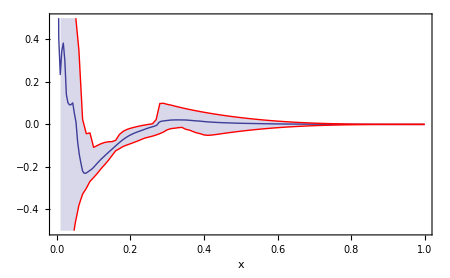

```mathematica
Show[Plot[0.25/1 Mean[Table[1/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+4/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{i,1,100}]],{x,0.001,1},PerformanceGoal->"Speed",PlotRange->{-0.5,0.5},ImageSize->{450,300},Frame->True,PlotPoints->30,BaseStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],AxesOrigin->{0,0},FrameLabel->{"x","","M_j/M∑e_q^2h_1(x),neutron",""},LabelStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],FrameTicks->{Automatic,Automatic,None,None},Epilog->{(*Text["9% th. unc.",{-5,0.31}],Text["Preliminary",{-5,0.45}]*)}],ListPlot[{Mjh1SumNeutMax,Mjh1SumNeutMin},PlotRange->{-0.5,0.5},Joined->True,Frame->True,PlotStyle->Red,Filling->{1->{2}}]]
```

### Tensor charge and violation of BC sum rule

```mathematica
Inth1Prot=Table[NIntegrate[4/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+1/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{x,0,1},AccuracyGoal->10^-2],{i,1,100}]
```

{0.201386,0.271032,0.0926731,0.354154,0.11544,0.281553,0.1751,0.288614,0.243724,0.31717,0.180317,0.0539547,0.39382,0.403875,0.327603,0.108004,0.246672,0.213243,0.391219,0.155793,0.256948,0.143169,0.228315,0.182968,0.134344,0.241827,0.0988447,0.29177,0.337271,0.384343,0.221807,0.217671,0.31835,0.254328,0.321722,0.144401,0.453517,0.27175,0.178363,0.159318,0.41593,0.150704,0.368992,0.330806,0.231239,0.213983,0.106827,0.214711,0.411716,0.286358,0.150902,0.400416,0.294258,0.242735,0.344545,0.214232,0.330054,0.273841,0.33153,0.292428,0.121596,0.306847,0.123432,0.332043,0.364476,0.293724,0.47119,0.155247,0.196471,0.266606,0.195186,0.001931,0.320935,0.297722,0.356008,0.142884,0.276897,0.290349,0.325842,0.203613,0.268874,0.159415,0.370525,0.186845,0.254144,0.227041,-0.0609641,0.424086,0.268435,0.204265,0.376808,0.246026,0.367429,0.356973,0.275091,0.292062,0.332591,0.216218,0.0225666,0.159707}

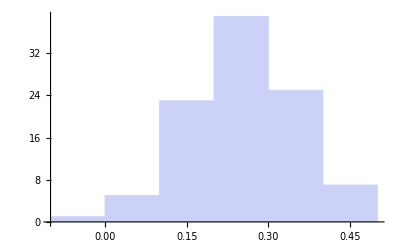

```mathematica
Histogram[Inth1Prot]
```

```mathematica
Table[NIntegrate[1/9(Tanh[√x(auv+buv x+cuv x^2+duv x^3)]/.FitReplex[[i]])xuv$SBDSSVLO[x]/x+4/9(Tanh[√x(adv+bdv x+cdv x^2+ddv x^3)]/.FitReplex[[i]])xdv$SBDSSVLO[x]/x,{x,0,1},AccuracyGoal->10^-2],{i,1,100}]
```

{-0.176437,-0.0869573,-0.397319,0.1029,-0.0797766,-0.0354029,0.0781151,0.0224875,-0.0591292,-0.215446,-0.152618,-0.508398,0.388409,0.39141,0.0373858,-0.163024,0.221717,0.133038,0.218328,0.0673172,-0.0236769,-0.0376002,-0.163925,-0.191669,-0.430394,-0.0628221,-0.0772372,-0.100476,-0.0787423,-0.0555299,-0.0625565,0.0130517,0.0349609,0.012933,-0.209067,-0.00807643,0.176663,-0.113635,0.00400794,-0.138596,0.163206,0.0794564,-0.0155207,-0.0115087,-0.0771691,-0.0825764,-0.186605,-0.0434083,0.166222,0.14562,-0.0530388,0.390545,0.117244,-0.0263239,0.110893,-0.0963254,-0.132138,0.131753,0.141994,0.0452799,-0.238529,0.185971,-0.200668,0.0875076,0.0108333,-0.0241764,0.130572,-0.012179,-0.0529462,0.0936006,-0.170952,-0.518678,0.219931,0.0239788,-0.12938,-0.156077,-0.225514,-0.0452313,0.144748,-0.118414,0.357414,-0.144898,0.109092,-0.0981194,-0.368186,0.126203,-0.227855,0.245068,0.0835621,-0.00512791,0.0414752,-0.158885,0.0956627,-0.0919952,-0.0782679,0.00733998,0.0790266,0.00678751,-0.127365,-0.226435}

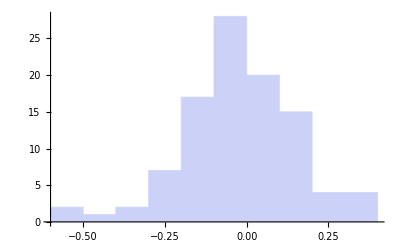

```mathematica
Histogram[Inth1Neut]
```